# Analisi dell’andamento del tempo di autocorrelazione in prossimità del punto critico e calcolo dell’esponente dinamico z

## Introduzione

Un argomento di grande interesse nel campo della meccanica statistica è lo studio delle transizioni di fase, cioè lo studio del processo di trasformazione di un sistema termodinamico da uno stato di aggregazione ad un altro. Lo studio di tali fenomeni richiede lo sviluppo di modelli capaci di descrivere l’interazione a distanza tra i vari elementi che compongono il sistema, tra questi il modello di Ising,elaborato da Ernst Ising nel 1925,  è a tutt’oggi uno dei modelli  meglio compresi e studiati. Tuttavia, nonostante i notevoli progressi compiuti negli ultimi decenni, una soluzione analitica del modello in 3  o più dimensioni  non è stata ancora individuata e allo stato attuale soltanto le teorie di campo medio e le simulazioni numeriche svolte con l’ausilio di un computer permettono di investigare il comportamento di tali sistemi in prossimità del punto critico. Nel nostro caso ci limiteremo ad un’analisi dell’andamento del tempo di autocorrelazione della magnetizzazione in un semplice sistema di Ising bidimensionale simulato tramite tecniche Monte Carlo al variare della temperatura e delle dimensioni lineari del sistema. La scelta di limitare la nostra analisi ad un sistema bidimensionale ci permetterà in seguito di confrontare i risultati ottenuti dalle simulazioni numeriche con quelli previsti dalla soluzione analitica del sistema fornita da Onsager nel 1944.

## 1 Il modello

La premessa essenziale alla base del modello di Ising è che le proprietà magnetiche di un materiale scaturiscano dall’interazione dei momenti magnetici generati dai tantissimi atomi impachettati all’interno del materiale stesso. Inizialmente ideato per descrivere un corpo magnetizzato a partire dai suoi costituenti elementari, il modello è stato poi impiegato per descrivere fenomeni variegati, accomunati dalla presenza di singoli componenti che interagendo gli uni con gli altri producono effetti collettivi. Esso è definito su un insieme discreto di variabili s_i, libere di assumere i valori +1 o −1, che costituiscono i nodi di un reticolo. Ciascuna  variabile rappresenta un atomo il cui momento magnetico o “spin” è allineato in una delle due sole direzioni ammesse. In un magnete reale gli spin interagiscono tra loro attraverso l’accoppiamento dei momenti magnetici nucleari  (teoria RKKY), Ising simula queste interazioni inserendo all’interno della hamiltoniana termini proporzionali al prodotto s_i s_j  degli spin. Nella sua forma più semplice le interazioni sono tutte della stessa forza J e agiscono solo tra gli spin primi vicini, in tal caso l’Hamiltoniana di un sistema di questo tipo costituito da N spin assume la forma:

H= -J ∑_(<i j>) s_i s_j - B ∑^N s_i,

dove con la notazione <ij> abbiamo indicato che la somma agisce solo sui primi vicini.
La funzione di partizione del sistema a sua volta può essere scritta come

Z=∑_{s_i} e^-βH,

dalla quale è possibile ottenere tutte le grandezze caratteristiche del sistema come energia interna U,energia libera F , entropia S e magnetizzazione totale del sistema M attraverso le relazioni

(U=-1/Z (∂ Ln Z)/(∂β)
S= -k β  (∂ ln Z)/(∂β)+ k*ln Z
F= U -T*S
⟨M⟩=(∂F)/(∂B)),

dove con k si è indicata la costante di Boltzmann.Spesso però, quando si sta effettuando una simulazione numerica di un sistema, risulta più utile calcolare  <m>, cioè la magnetizzazione media per spin, direttamente dalla media sui singoli spin:

⟨m⟩ = 1/N⟨∑_i s_i⟩.

Tale funzione prende il nome di parametro d’ordine del sistema perchè segnala il passaggio del sistema da una fase disordinata paramagnetica caratterizzata da alti valori della temperatura T ad una nuova fase ordinata  ferromagnetica a bassi valori della temperatura. Un’altra grandezza spesso utilizzata per individuare  transizioni di fase all’ interno del sistema è la cosiddetta suscettività magnetica  χ, definita come la derivata rispetto al campo B della funzione m(t)

χ=(∂⟨m⟩)/(∂B),

che può essere intesa come una misura della risposta di m al variare del campo B. In un sistema di Ising, poichè  solo la funzione m(T) risulta continua e non la sua derivata,  si parla di transizione di fase del secondo ordine o continua. La temperatura alla quale si verifica il passaggio da una fase all'altra prende il nome di Temperatura di Curie e  per un sistema bidimensionale risulta essere pari a circa

T_c= (2j)/(k ln(1+√2))≃2.27J.

## 2 Metodi Monte Carlo

Come già accennato precedentemente sono pochi i casi in cui  è possibile calcolare analiticamente la funzione di partizione del sistema, nella maggioranza di essi si è costretti ad utilizzare teorie approssimate o simulazioni numeriche.
Con la locuzione “metodi Monte Carlo”  si indica un’ampia classe di metodi computazionali che sfruttano  ripetuti campionamenti casuali per ottenere soluzioni numeriche di problemi che sono troppo complicati per essere risolti in maniera analitica. Essi si basano su algoritmi che all’equilibrio generano una serie di stati che segue la distribuzione di probabilità che si suppone abbia il fenomeno da indagare. Durante la simulazione il computer calcola ad ogni step un possibile stato  ed  esegue su di esso delle misure delle quantità di interesse ,memorizzando i risultati in un buffer. 
L’evoluzione dinamica del sistema simulato è governata da un processo di Markov caratterizzato da una matrice M scelta in modo tale da garantire l’ esistenza per t→∞ di una distribuzione di equilibrio pari a quella del sistema reale. Il passaggio da uno stato del sistema μ ad uno stato successivo ν   è regolato da una  probabilità P(μ →ν),detta probabilità di transizione, memorizzata all’interno della matrice M. Le probabilità P sono scelte in modo tale da verificare le seguenti particolari condizioni:

non devono variare nel tempo.

devono dipendere solamente dalle proprietà degli stati ν e μ e non dagli stati precedentemente attraversati dal sistema.

dato uno stato di partenza μ , la somma su tutti i possibili  altri stati ⋁ deve essere pari ad uno:  ∑_ν P(μ→ν) =1.

In aggiunta a ciò, altre due condizioni devono essere soddisfatte dalla matrice M: essa deve essere ergodica e deve soddisfare il principio del bilancio dettagliato.
La condizione di ergodicità assicura che sia sempre possibile partendo da uno stato μ raggiungere qualsiasi altro stato ν in un tempo sufficientemente lungo. Questa condizione è necessaria se vogliamo ottenere una distribuzione di probabilità finale in cui ogni stato possiede una probabilità non nulla.
La seconda condizione,detta del bilancio dettagliato, impone il rispetto dell’equazione:

p_μ P(μ→ν) = p_ν P(ν→μ),

e assicura che una volta raggiunta la distribuzione finale degli stati ogni processo elementare è equilibrato dal suo opposto

(P(μ→ν))/(P(ν→μ))= (g(μ→ν)A(μ→ν))/(g(ν→μ)A(ν→μ))=p_μ/p_ν,

dove le P(μ→ν) sono state riscritte come il prodotto di una probabilità di selezione g(μ→ν) e di un rapporto di accettazione A(μ→ν), il cui valore può variare tra 0 e 1. Il rapporto di accettazione  garantisce che se partiamo da uno stato μ e un nuovo stato ν viene generato, questo viene accettato una frazione di volte pari ad A(μ→ν), lasciando il sistema nello stesso stato μ in caso contrario. Questa procedura lascia ampia libertà nella scelta delle probabilità di selezione  g(μ→ν), che possono assumere qualsiasi valore  compatibile con l’equazione (8). Valori troppo bassi del rapporto di accettazione tuttavia influenzano negativamente l’efficienza dell’algoritmo in quanto molti dei nuovi stati creati dalla macchina sono rigettati. Un modo di risolvere questo problema è di fissare  le probabilità di selezione g quanto più vicine possibili alle probabilità di transizione P richieste e di porre il maggiore dei due rapporti di accettazione A pari ad 1 ,dando al secondo qualsiasi valore sia necessario per verificare l’equazione (8). Come risulta allora evidente le condizioni imposte sulla matrice di Markov di fatto non determinano del tutto la forma della transizioni di probabilità, al contrario esse garantiscono una certa libertà nella costruzione del processo di Markov che determina l’evoluzione dinamica del sistema, ciò si traduce nella possibilità di generare algoritmi diversi adatti alle più diverse applicazioni. Mostriamo ora con maggior dettaglio l’algoritmo proposto da Metropolis.

2.1 L’algoritmo di Metropolis

L’algoritmo Metropolis è il più famoso ed utilizzato algoritmo Monte Carlo al mondo, fu presentato per la prima volta da Nicolas Metropolis in un articolo del 1953 sulla simulazione di un gas costituito da 224 particelle. In esso le probabilità di selezione g(μ→ν) per ciascuno degli stati raggiungibili sono tutte uguali e differenti da zero mentre quelle relative a stati non raggiungibili sono poste pari a zero.
Ad esempio, supponendo di voler simulare un sistema costituito da N spins con una dinamica single-spin-flip, avremo N possibili stati ν (incluso lo stato iniziale) che possono essere raggiunti da un dato stato iniziale μ, ciascuno dei quali generato dalla rotazione di un singolo spin del sistema e che differiscono per energia al più di un valore pari a 2J per ciascuno dei primi vicini dello spin invertito. Di conseguenza ci sono N probabilità di selezione g(μ→ν) non nulle, ciascuna delle quali pari a

g(μ→ν)=1/N.

Con queste probabilità di transizione, la condizione di bilancio dettagliato assume la forma

(P(μ → ν))/(P(ν→μ))= (A(μ → ν))/(A(ν→μ))= ⅇ^(-β(E_ν-E_μ)).

A questo punto fissiamo i rapporti di accettazione in modo tale da soddisfare l’equazione del bilancio dettagliato. Seguendo il suggerimento esposto nella precedente sezione  e supponendo sia μ lo stato ad energia più bassa ( e quindi più probabile), fissiamo

A(μ → ν) =Piecewise[{{ⅇ^(-β(E_ν-E_μ)), se E_ν-E_μ> 0}, {1, altrimenti}}].

A prima vista l’algoritmo può sembrare oneroso dal punto di vista computazionale perchè richiede di calcolare ad ogni step la differenza tra il  valore dell’energia complessiva del nuovo stato e quella posseduta precedentemente dal sistema, ma in realtà si può aumentare la velocità di esecuzione della simulazione notando che non è necessario sommare su tutti gli spin ad ogni step ma basta sommare sui primi vicini dello spin invertito, in quanto

E_ν-E_μ = 2J∑_(i p.v. di k) s_i^μ s_k^μ= 2J s_k^μ ∑_(i p.v. di k) s_i^μ,

Dove abbiamo indicato con s_k lo spin invertito.

Struttura del reticolo

Oltre che dalla hamiltoniana il comportamento del sistema è determinato anche dalla struttura del reticolo adottato, dalla quale dipende come ciascun sito è collegato ai suoi vicini.
Nel nostro caso ci limiteremo ad utilizzare un semplice reticolo quadrato caratterizzato da una dimensione laterale L inizialmente pari a 20; Successivamente, quando saranno considerati gli effetti di scala, tale dimensione sarà variata più volte e le misure nuovamente ripetute. 
Un secondo problema da affrontare prima ancora di avviare la simulazione e strettamente legato al primo  è quello di fissare le condizioni al bordo, vale a dire specificare con chi confinano gli spin posti sul bordo del reticolo in modo da poter approssimare il comportamento di un sistema infinito. Normalmente si introducono semplici condizioni al bordo periodiche allo scopo di garantire che tutti gli spin abbiano lo stesso numero di coordinazione e la stessa struttura locale. 
Un’alternativa più efficiente è data dalle “helical boundary conditions” che sono più semplici da implementare e rendono l’ esecuzione leggermente più veloce. Gli spin in questo caso sono memorizzati in un array S monodimensionale di dimensioni L^2,in modo tale che il valore dello spin i-esimo sia accessibile nella posizione S[i] e suoi  primi vicini nelle posizioni  (i±1)mod L^2 e (i±L) mod L^2.
Infine é necessario fissare una temperatura T iniziale alla quale far partire la simulazione. Le due scelte più comuni sono quelle di fissare o T= 0 oppure T= ∞ (scelta da noi adottata). Al primo caso corrisponde un sistema posto nel suo stato fondamentale con tutti gli spin allineati in un verso o nell’altro; nel secondo caso l’ energia termica disponibile è talmente elevata da rendere irrilevante la variazione di energia totale indotta dalla interazione tra gli spin, cosi questi si presentano disposti in maniera totalmente casuale. Queste due scelte sono le più comuni perchè  corrispondono a due stati del sistema noti e sono semplici da generare, tuttavia c’è una terza alternativa particolarmente utile quando si effettuano diverse simulazioni a diverse temperature in serie tra loro. In questo caso infatti conviene utilizzare come stato iniziale di una simulazione lo stato finale della simulazione precedente in quanto ciò permette di ridurre il tempo richiesto dall’algoritmo per giungere alla distribuzione di stazionarietà.

## Il tempo di autocorrelazione e la funzione di autocorrelazione

Una volta fissata la configurazione iniziale ed aver avviato la simulazione con le impostazioni desiderate è necessario calcolare  il tempo di autocorrelazione τ del sistema  al fine di poter stimare il numero di campionamenti indipendenti che è possibile estrarre dall’intera sequenza di dati accumulati. Sommariamente possiamo dire che τ  fornisce una misura del tempo richiesto dal sistema per passare da uno stato ad una nuova configurazione  significativamente differente da quella originale.
Esistono diversi modi di stimare τ, il più semplice è quello di assumare il suo valore pari al tempo di equilibrio τ_eq, in quanto di solito il tempo di equilibrio è considerevolmente più lungo del tempo di correlazione. La spiegazione di tale comportamento sta nel fatto che uno stato vicino all’equilibrio è qualitativamente più vicino ad un altro stato ottenuto all’equilibrio che ad uno stato generato nelle fasi iniziali della simulazione, quando il sistema è ancora distante dalla distribuzione limite. Si tratta tuttavia  di una stima abbastanza rozza che può essere migliorata calcolando la funzione di autocorrelazione temporale di una grandezza caratteristica del sistema e ricavando il tempo di autocorrelazione da quest’ultima.

La funzione di autocorrelazione della magnetizzazione

La  funzione di autocorrelazione normalizzata ϕ_m(t) della magnetizzazione è definità come :

ϕ_m(t) =[⟨m(0)m(t)⟩ -⟨m⟩^2]/[⟨m^2⟩-⟨m⟩^2].

Tale funzione risulta essere  pari ad 1 a t = 0 e decade a 0  per t→ ∞ con un comportamento asintotico di tipo esponenziale

ϕ_m(t) → ⅇ^(-(t/τ_exp)).

il parametro τ_exp cosi definito è il tempo di correlazione esponenziale del sistema e diverge per T→ T_c . 
La ϕ(t) misura la correlazione  tra i valori assunti dalla magnetizzazione a due diversi istanti t e t'+t sul reticolo. Se misuriamo la differenza tra la magnetizzazione m(t') al tempo t' e il suo valore medio e  poi ripetiamo l’operazione per un istante t'+t e moltiplichiamo insieme i risultati otteniamo un valore positivo se la magnetizzazione fluttua nella stessa direzione, negativo nel caso opposto. Nel caso di una simulazione basata sull’algoritmo Metropolis con un implementazione del tipo single spin flip è chiaro che se misuriamo la magnetizzazione in due stati separati da un singolo microstep, i due valori saranno strettamente  correlati e l’autocorrelazione assumerà valori positivi. Al contrario, se i due stati del sistema sono separati da un gran numero di microstep i risultati saranno totalmente scorrelati e l’autocorrelazione assumerà valori prossimi allo zero. Una volta calcolati i valori assunti dalla ϕ(t) per  successivi step della simulazione risulta semplice individuare  il valore di τ_exp tramite un fit non lineare. Purtroppo il valore cosi ricavato di τ_exp è estremamente sensibile all’intervallo su cui è esteso il fit e il punto esatto in cui questo viene interrotto può avere grandi effetti sul valore di τ stimato. 
Un secondo tempo di rilassamento del sistema, il cosiddetto tempo  di autocorrelazione integrato, è definito a partire dall’integrale della funzione ϕ(t)  come

τ_int= (∫_0)^∞ϕ(t)ⅆt,

che in caso di step discreti si traduce in

τ_int=1+∑_(t=1)^∞ ϕ(t).

Questa quantità risulta essere di grande importanza per la determinazione degli errori e diverge con lo stesso esponente dinamico del tempo di rilassamento esponenziale τ. 
Il tempo integrato τ_int, seguendo la definizione, dovrebbe essere calcolato sommando su un numero infinito  di step, in realtà ciò è impossibile da fare in quanto le misure di ϕ(t) cominciano ad essere sovrastate dal rumore per t >> τ_int. Per questo motivo ci si limita  a calcolare τ_int su un numero limitato M di misure ottenute dalla simulazione una volta che questa abbia raggiunto la distribuzione di equilibrio. Questa approssimazione introduce un bias sulla stima di τ_int

bias((τ̂)_int)=-(∑ ϕ(t))_(|t| > M)^∞+ o(1/n)

ed influenza la varianza associata ad essa associata

var((τ̂)_int)=(2(2M+1))/n* τ_int^2.

Un alto valore di M fornisce un bias inferiore ma in compenso fa crescere la varianza, viceversa un valore basso di M  permette di diminuire il bias a discapito della varianza. Un conveniente algoritmo per individuare una valida finestra di valori da utilizzare è stato proposto da Sokal(1996) e consiste nello scegliere il  più piccolo intero M tale che M ≥ c τ(M), dove c è una costante fissata da scegliere opportunamente. Nel caso di un andamento di ϕ(t) puramente esponenziale è sufficiente porre c = 4, altrimenti ,quando ad esempio la funzione di autocorrelazione ϕ(t)  presenta un decadimento più lento di una esponenziale, conviene porre c almeno pari a 6 , 10 se possibile.

slowing down critico

Nella regione vicina al punto critico T_c , detta regione critica, il sistema tende a creare grandi clusters di  atomi disposti nella stessa direzione. Questi clusters contribuiscono significativamente sia alla magnetizzazione sia all’energia complessiva del sistema e generano grandi fluttuazioni, dette a loro volta  fluttuazioni critiche, nei valori  dei parametri del sistema quando invertono i valori dei loro spin. La magnitudine di queste fluttuazioni, dipendendo dal valore di ξ , diverge all’avvicinarsi del punto critico e di conseguenza anche suscettività e calore specifico,  legate ad esse dalle relazioni di fluttuazione-dissipazione, assumono lo stesso andamento. Questi interessanti comportamenti, tipici della regione critica, sono detti fenomeni critici e sono stati oggetto di intensi studi, molti dei quali svolti proprio con l’ausilio dei metodi Monte Carlo. Sfortunatamente  la regione critica è proprio l’area dove  l’algoritmo Metropolis risulta meno efficiente e accurato. I motivi per cui questo accade  sono essenzialmente due: Il primo, del tutto generico e non dipendente dal particolare algoritmo usato, risulta essere legato alle stesse fluttuazioni critiche in quanto gli errori statistici sulle misure sono legati alle dimensioni delle fluttuazioni, cosicchè  quanto più grandi sono quest’ultime tanto maggiori sono gli errori commessi.
Un modo per ridurre gli errori commessi sulle misure consiste nel prolungare la simulazione e mediare su un numero più elevato di misure indipendenti ma ciò è reso molto difficile dall’insorgere del secondo problema:  l’aumento del tempo di correlazione τ della simulazione;  Infatti, come la suscettività magnetica e il calore specifico, il tempo di correlazione su un modello di Ising infinito diverge all’avvicinarsi al punto critico T_c. Questo fenomeno, noto come slowing down critico, rende difficile ottenere grandi quantità di misure indipendenti e insieme alle fluttuazioni contribuisce all’aumento degli errori associati alle misure.  A differenza però dell’aumento delle dimensioni delle fluttuazioni, l’aumento del tempo di correlazione varia a seconda del particolare algoritmo utilizzato e risulta particolarmente elevato per una simulazione di tipo Monte Carlo basata su un implementazione di tipo single spin flip dell’algoritmo Metropolis.
Per descrivere la divergenza del tempo di correlazione τ vicino la transizione di fase  definiamo un nuovo esponente critico z, denominato esponente dinamico, tale che

τ∼ |t|^-zν per  t ~ 0,

dove ν è l’ esponente critico della lunghezza di correlazione ξ e t è una quantità adimensionale legata alla temperatura secondo la seguente relazione

t= (T-T_c)/T_c.

Ricordando  che nei pressi del punto critico  ξ(t) ~ t^-ν   e combinando questo risultato con l’ equazione (19) è possibile esprimere τ in funzione della lunghezza di correlazione ξ.

τ∼ ξ^z.

Questa equazione ci dice che poichè la lunghezza di correlazione ξ diverge al punto critico lo stesso dovrebbe fare  τ,  ma ciò in realtà non accade in un sistema finito, dove la lunghezza di correlazione  è limitata dalle dimensioni lineari del sistema stesso. Di conseguenza per tutte le temperature sufficientemente vicine alla temperatura critica l’equazione (19) assume la forma

τ∼Min(ξ,L)^z.

La conseguenza diretta di questo fenomeno è la scomparsa della discontinuità di τ   nei pressi punto critico T_c:  essa infatti non  presenta più la divergenza tipica dei sistemi infiniti ma raggiunge un valore massimo finito,oltrepassato il quale tende nuovamente a descrescere. Nel caso dell’ algoritmo Metropolis è stato stimato un valore dell’esponente dinamico maggiore di  2.

L’algoritmo di Wolff

Come abbiamo potuto vedere, la ragione principale del grande valore di τ nell’algoritmo Metropolis è la divergenza della correlazione e le fluttuazioni critiche presenti nei pressi della temperatura critica. Quando la lunghezza di correlazione diventa grande, vicino a t_c, grandi regioni in cui tutti gli spin sono allineati si  formano all’ interno del reticolo. é molto difficile per un algoritmo basato sulla tecnica del single spin flip capovolgere queste regioni perchè deve farlo lavorando su un singolo spin alla volta  e ogni mossa ha un alta probabilità di essere rigettata; ad esempio in due dimensioni invertire un singolo spin circondato da spin allineati nello stesso verso costa 8J di energia e la probabilità che tale mossa venga accettata non  è superiore al 3%. l’algoritmo risulta così estremamente inefficiente. Una soluzione a questo problema fu proposta nel 1989 da Ulli Wolff basandosi su un precendente lavoro di Swendsen e Wang. L’algoritmo di Wolff rientra nella categoria dei cluster-flipping algorithms, cioè di quella classe di algoritmi che non invertono un singolo spin alla volta bensi interi cluster individuati durante i singoli step. Il vantaggio principale di questo tipo di algoritmi è che  al prezzo di una maggiore complessità computazionale sono in grado di eliminare quasi del tutto il fenomeno dello slowing down critico . Il problema principale da affrontare per poter implementare una soluzione di tale tipo è quello di  individuare il cluster da invertire ad ogni singolo step. Chiaramente, poichè la dimensione dei cluster varia con la temperatura, l’algoritmo deve possedere una dipendenza da T che permetta di variare la dimensione media dei cluster costruiti ,riducendoli alle alte temperature a piccoli gruppi di spin o, al limite, al singolo spin. Possiamo ottenere un risultato del genere costruendo i cluster partendo da uno spin scelto casualtmente, legando a quest’ultimo gli spin primi vicini con una probabilità P_add scelta opportunamente e  ripetendo poi il procedimento per ognuno degli spin cosi aggiunti. Quando non ci sono più spin da aggiungere il cluster  viene invertito  con un rapporto di accettazione  che dipende dall’energia richiesta per l’inversione.  Rimane  ora da individuare quale valore dare a P_add affinchè l’algoritmo  fornisca risultati adeguati. A questo scopo consideriamo due stati μ e ν che differiscono tra loro soltanto per l’inversione di un singolo cluster ai bordi del quale  alcuni spin sono rivolti nella stessa direzione degli spin all’interno del cluster altri invece sono disposti nella direzione contraria.
 Supponiamo ora di effettuare un update del sistema che ci porta dallo stato μ allo stato ν. Esistono molte possibili mosse di questo tipo, potremmo ad esempio scegliere uno qualsiasi degli spin del cluster come spin iniziale e poi aggiungere i restanti spin in un ordine qualsiasi. Per il momento però consideriamo una sola particolare mossa caratterizzata da un particolare spin iniziale e da una particolare sequenza di aggregazione degli spin del cluster. La probabilità di scegliere un dato seme è la stessa sia nella trasformazione μ→ν sia nella trasformazione contraria, l’ unica cosa che cambia nei due casi è il numero di bond ai bordi che vengono creati e distrutti ai bordi del cluster. Supponiamo che per la prima trasformazione  sia necessario distruggere m bonds e crearne n, ai primi corrispondono m spin allineati a quelli interni al cluster che non sono stati aggiunti ad esso , ai secondi invece n spin antiallineati a quelli del cluster.   La probabilità di  non aggiungere un singolo spin al cluster è pari a 1- P_add, di conseguenza  la probabilità di non aggiungere m spin nella trasformazione μ→ν , che è proporzionale alla probabilità di selezione g(μ→ν), risulta essere pari a (1-P_add )^m. Nella trasformazione inversa invece  è necessario distruggere n bonds e di conseguenza la probabilità di non aggiungere gli n spin allineati al cluster è pari a  (1-P_add )^n e a sua volta risulta proporzionale a g(ν→μ). La condizione del bilancio dettagliato a questo punto diventa

(A(μ → ν)g(μ→ν))/(A(ν→μ)g(ν→μ))=(A(μ → ν))/(A(ν→μ) ))*(1-P_add)^(m-n)= ⅇ^(-β(E_ν-E_μ)),

dove A(μ → ν) e A(ν→μ) rappresentano i rapporti di accettazioni delle due differenti trasformazioni. La differenza di energia E_μ - E_ν  dei due stati a sua volta dipende dal numero di bond rotti nel passare da uno stato all’altro: per ognuno degli  m bond rotti da per passare da μ a ν si ha una variazione di energia pari a +2J, mentre per ciascuno degli n bond creati per andare da  μ  a ν si ha una variazione di energia pari a -2J. La variazione totale di energia sarà quindi pari a  2J(m-n). Sostituendo questo risultato nell’equazione 13 si ottiene

(A(μ → ν))/(A(ν→μ) )) = [ⅇ^(2βJ)(1-P_add)]^(n-m).

A questo punto basta notare che ponendo P_add pari a 1- e^(-2βJ) otteniamo che il rapporto dei rapporti di accettazione risulta essere sempre pari a 1, indipendentemente dalle proprietà degli stati μ e ν. Ciò significa che con questa scelta possiamo porre i rapporti di accettazione per ogni trasformazione pari ad 1, ottenendo  la migliore efficienza possibile per l’ algoritmo.
Oltre al principio del bilancio dettagliato l’ algoritmo deve soddisfare anche il criterio dell’ ergodicità precedentemente discusso. Tale condizione però è evidentemente soddisfatta dal momento che  c’è una possibilità non nulla ad ogni step che ciascun spin sia scelto come singolo membro del cluster e tale possibilità garantisce che partendo da una data configurazione sia possibile giungere a qualsiasia altra configurazione in un numero limitato di step.

## Misure

Allo scopo di confrontare le previsioni teoriche con i dati forniti dalla nostra simulazione è stato inizialmente simulato un modello di Ising (j=1) su un reticolo di dimensioni lineare L = 40 per 11 diverse temperature comprese nell’ intervallo 1,4-3,5. Dai dati raccolti  per ciascuna delle temperature è stata calcolata la  funzione di autocorrelazione della magnetizzazione, dalla quale sono stati poi ricavati i valori di τ_exp e τ_int del sistema. I risultati ottenuti infine sono stati plottati su un grafico cartesiano in funzione della temperatura allo scopo di evidenziarne l ‘andamento nei pressi della temperatura critica. Nella seconda parte le misure sono state ripetute per diversi valori di L ad una temperatura prossima alla temperatura critica e dai dati raccolti è stata calcolato l’esponente dinamico z del sistema.

Grafico dei tempi di equilibrio

Riportiamo qui di seguito i grafici che mostrano l’andamento del valore della magnetizzazione per spin al variare del tempo per un modello di Ising bidimensionale caratterizzato da una dimensione lineare L = 40. È facile notare come al di sotto del punto critico il modello raggiunga l’equilibrio  in un tempo variabile compreso tra i 100 e i 1000 sweeps.  Per temperature superiori a T_c   esso rimane in una fase disordinata e di conseguenza risulta più difficile individuare  il tempo di equilibrio τ_eq del sistema. Un espediente che adotteremo per tutte le  misure sarà quello di trascurare i primi 3000000 microstep della simulazione  anche per sistemi di dimensioni inferiori, in modo da dare al sistema il tempo necessario affinchè esso superi la fase transiente e raggiunga l’equilibrio.

-Graphics-

Grafico dell’ andamento del tempo di autocorrelazione esponenziale τ_exp al variare della temperatura

L’andamento del tempo di autocorrelazione esponenziale  al variare  della temperatura  mostra un picco nella area caratterizzata da temperature T comprese tra 2,2 e 2,3 , in accordo con quanto predetto dalla soluzione analitica per la quale T_c = 2,27.

Grafico dell’ andamento del tempo di autocorrelazione integrato τ_int al variare della temperatura

-Graphics-

Anche τ_int mostra un picco nell’area compresa tra 2,1 e 2,3 in accordo con quanto previsto dalla soluzione analitica e con la stime di τ_exp.

Andamento del tempo di autocorrelazione τ al variare di L nei pressi del punto critico T_c del sistema con algoritmo Metropolis

Allo scopo di  ottenere una stima dell’ esponente critico z abbiamo simulato il modello di Ising alla temperatura critica T_c per 6 diversi valori di L  compresi tra 10 e 35 e separati da step di 5. Applicando la funzione logaritmo ai dati cosi ottenuti è stato possibile eseguire un fit lineare  e ricavare  il valore di z  ricercato dalla pendenza della retta di regressione

Ln(τ) = z Ln(L).

Il primo metodo, basato sul calcolo del tempo di correlazione esponenziale, ha fornito una stima di z pari a circa  2,49 ± 0.04 σ, un valore superiore a quello atteso  pari a circa 2.2 . Si tratta tuttavia di un metodo estremamente sensibile a variazioni dell’intervallo su  cui si sono eseguiti i fit per il calcolo dei valori di τ_exp e per questo  la stima è da ritenersi poco precisa.

Il secondo metodo invece ha fornito  un valore  di z pari a circa 2.4 ± 0.1σ, anch’esso superiore a quello atteso  ma caratterizzato da una deviazione standard più alta.

Andamento del tempo di autocorrelazione τ al variare di L nei pressi del punto critico T_c del sistema con algoritmo Wolff

Le misure sono state successivamente ripetute per 5 diversi valori di L comrpesi da 15 e 30 e separati da step di 5 implementando l’algoritmo di Wolff.Le misure in questo caso, sebbene vicine ai risultati riportati in letteratura , risultano  inferiori a quelli attesi, fornendo valori pari a 0,07  per τ_exp e 0,29 ±0.01 per τ_int

## Conclusioni

I dati raccolti mostrano un sensibile aumento dei tempi di correlazione integrale e esponenziale all’ avvicinarsi al punto critico T_c, evidenziando cosi il fenomeno dello slowing down critico che affligge l’ algoritmo Metropolis nei pressi della temperatura critica. Nella seconda parte di questa esperienza abbiamo verificato  come  τ, oltre  a dipendere dalla temperatura,  scali con L con un esponente critico superiore a 2. L’ aumento delle risorse hardware necessarie per calcolare τ_int su sistemi di dimensioni lineari  maggiori  di quelle precedentemente elencate  ci ha purtroppo impedito  di ottenere  misure più precise dell’ esponente dinamico z.

# Sorgente

variabili globali

```mathematica
ClearAll["Global`*"]
$HistoryLength=4 ; (*per ridurre impatto su memoria*)

γ= 7/4;
d=2;
ν=1;
```

pacchetti richiesti

```mathematica
Needs["CCompilerDriver`"]
Needs["ErrorBarPlots`"]
```

algoritmi Metropolis e Wolff e funzioni per il calcolo della autocorrelazione e dell’esponente critico

### funzione di autocorrelazione

```mathematica
funautocor [magn_List]:=CorrelationFunction[magn,{Length@magn-1}]
```

### algoritmo di windowing di Sokal

```mathematica
sokal[autocor_List,impostazioni_List, espdinamico_:0]:=Block[{c=10,sokalaut,test,range,dimensione1,dimensione2,sum,pos,poss,dati},
If[espdinamico==0,
range=RotateLeft@Reverse@Range[Dimensions[autocor][[2]]] ;
dimensione1 =  Dimensions[autocor][[1]]; 
dimensione2 =  Dimensions[autocor][[2]] ;
sokalaut=autocor[[;;,1;;]]*dimensione2/ConstantArray[range,dimensione1];
sum= ParallelMap[(1+Accumulate[#[[1;;Floor[5/6 * dimensione2]]]])&,sokalaut]    ;

test=ParallelMap[Thread[#[[1]]>#[[2]]&[{Range[Floor[5/6 *dimensione2]],  c*sum[[#,;;Floor[5/6 *dimensione2]]]}]] &,Range[dimensione1]];
pos=Parallelize[Flatten[FirstPosition[#,True]]&/@test,Method->"FinestGrained"];
poss= Transpose[{Range[dimensione1],impostazioni[[;;,4]],Flatten@pos}] ;
poss = DeleteCases[poss,{_?NumberQ,_?NumberQ,_?MissingQ}];

dati = {  #[[2]]    ,

sum[[#[[1]],#[[3]]  ]]    ,

Sqrt[sum[[  #[[1]],#[[3]]    ]]^2 *(2*(2*#[[3]]+1))/dimensione2]    }&/@ poss;

N@dati,


dimensione1 =  Dimensions[autocor][[1]];
 range =Table[RotateLeft@ Reverse[ Range@Length[autocor[[i]]]],{i,1,dimensione1}];
dimensione2 = Table[Length@autocor[[i]]   ,{i,1,dimensione1}];

sokalaut =ParallelTable [autocor[[y,;;]]*dimensione2[[y]]/range[[y]]         ,{y,1,dimensione1}      ];

(*sum= ParallelMap[(1+2*Accumulate[#[[1;;Floor[3/4 *Length@#]]]])&,sokalaut]  ;*)
sum=ParallelTable[(1+Accumulate[sokalaut[[i,1;;Floor[5/6 * dimensione2[[i]]]]]  ]  )               ,{i,1,dimensione1}];
test=ParallelMap[Thread[#[[1]]>#[[2]]&[{Range[Floor[5/6 *dimensione2[[#]]]],  c*sum[[#,;;Floor[5/6 *dimensione2[[#]]]]]}]] &,Range[dimensione1]];

pos=Parallelize[Flatten[FirstPosition[#,True]]&/@test,Method->"FinestGrained"];
poss= Transpose[{Range[dimensione1],impostazioni[[;;,3]],Flatten@pos}]   ;
poss = DeleteCases[poss,{_?NumberQ,_?NumberQ,_?MissingQ}];
dati = {  #[[2]]    ,

sum[[#[[1]],#[[3]]  ]]    ,

Sqrt[sum[[  #[[1]],#[[3]]    ]]^2 *(2*(2*#[[3]]+1))/dimensione2[[#[[1]]]]]    }&/@ poss;

N@dati


]

]
```

### monte carlo con helical boundary conditions e algoritmo Metropolis

```mathematica
isingMC=Compile[{{steps,_Integer},{eqsteps,_Integer},{lato,_Integer},{temp,_Real}},Block[{matrix,β=1/temp,x,j=1, magnetizzazione,spinsum,delta,random,prob ,yes=0,area=lato^2,precalc,up,down,left,right,counter=1,scalare},
up=RotateLeft[Range[lato^2]]   ;   
         down=RotateRight[Range[lato^2]];
         left=RotateLeft[Range[lato^2],lato];
         right=RotateRight[Range[lato^2],lato];
prob[2]= ⅇ^(-(β*4)); 
prob[4]= ⅇ^(-(β*8));
 
magnetizzazione=ConstantArray[0,Ceiling[(steps-eqsteps+1)/area]];
matrix=Developer`ToPackedArray@RandomChoice[{-1,1},area];
precalc= Transpose[{up,down,left,right}];
scalare=Total@matrix ;
Do[
 
yes=0;
random =RandomReal[];
x=RandomInteger[{1,area}];
(*Compile`GetElement[matrix,down[[x]],y]*)

spinsum=Plus@@matrix[[precalc[[x]]]];

delta=   spinsum*matrix[[x]];
If[delta<=0,matrix[[x]] = - matrix[[x]];yes=1,
If[random < prob[delta], matrix[[x]]=-matrix[[x]];yes=1
]];
If[yes==1,
scalare= scalare+2*matrix[[x]]];
If[i<=eqsteps ,
magnetizzazione[[1]]=scalare
,


If[Mod[i-eqsteps,area]==0, magnetizzazione[[counter+1]]= scalare  ;++counter       ]
 

]
,{i,2,steps}];
 
N@magnetizzazione/lato^2

]
,RuntimeOptions->"Speed",CompilationTarget->"C"];
```

```mathematica
(*RepeatedTiming[isingMC[93000,7000,lato,2,up[lato],down[lato],left[lato],right[lato]]][[1]]*)
```

### monte carlo con periodic boundary conditions ( metropolis/microstep)

```mathematica
isingMcPBC=Compile[{{steps,_Integer},{eqsteps,_Integer},{lato,_Integer},{temp,_Real}},Module[{matrix,β=1/temp,x,y,j=1, magnetizzazione,spinsum,delta,random,prob ,yes=0,up,down,left,right,scalare,counter=1},
prob[2]= ⅇ^(-(β*4));
prob[4]= ⅇ^(-(β*8));
 up=RotateLeft[Range[lato]];
down=RotateRight[Range[lato]];
left=RotateLeft[Range[lato]];
right=RotateRight[Range[lato]];

magnetizzazione=ConstantArray[0,steps-eqsteps+1];
matrix=Developer`ToPackedArray@RandomChoice[{-1,1},{lato,lato}];
scalare=Total@Flatten@matrix ;
Do[
 
yes=0;
random =RandomReal[];
x=RandomInteger[{1,lato}];
y=RandomInteger[{1,lato}];

spinsum=Plus[

Compile`GetElement[matrix,down[[x]],y],Compile`GetElement[matrix,up[[x]],y],Compile`GetElement[matrix,x,left[[y]]],Compile`GetElement[matrix,x,right[[y]]]

];

delta=   spinsum*matrix[[x,y]];
If[delta<=0,matrix[[x,y]] = - matrix[[x,y]];yes=1,
If[random < prob[delta], matrix[[x,y]]=-matrix[[x,y]];yes=1
]];
If[yes==1,
scalare= (scalare+2*matrix[[x,y]])
];

If[i<=eqsteps ,
magnetizzazione[[1]]=scalare
,
 If[Mod[i-eqsteps,lato^2]==0, magnetizzazione[[counter+1]]= scalare  ;++counter       ]
]

,{i,2,steps}];
 
N@magnetizzazione/lato^2

]
,RuntimeOptions->"Speed",CompilationTarget->"C"]
```

CompiledFunction[…]

### monte carlo (wolff algorithm)

```mathematica
wolff=Compile[{{steps,_Integer},{eqsteps,_Integer},{side,_Integer},{temp,_Real}},Block[{helical,β=1/temp,i, prob ,area=side^2,up,down,left,right,stack,oldspin,sp,sl,current,magnetizzazione},
up=RotateLeft[Range[area]]   ;   
         down=RotateRight[Range[area]];
         left=RotateLeft[Range[area],side];
         right=RotateRight[Range[area],side];
helical=RandomChoice[{-1,1},area];
prob= 1-ⅇ^(-2β);
magnetizzazione=ConstantArray[0,steps-eqsteps];
 Do[
stack= ConstantArray[0,area];
i= RandomInteger[{1,area}];
       stack[[1]]=i;
oldspin= helical[[i]];
helical[[i]]=-helical[[i]];
sp=1;
sl=sp+1;
While[sp<sl,
 
current= stack[[sp]];
sp=sp+1;

If[helical[[up[[current]]]]== oldspin,
If[RandomReal[]<prob,
stack[[sl]]= up[[current]];
helical[[up[[current]]]]=-oldspin;
sl=sl+1;
]
];
If[helical[[down[[current]]]]== oldspin,
If[RandomReal[]<prob,
 
stack[[sl]]=down[[current]];
helical[[down[[current]]]]=-oldspin;
sl=sl+1;
]
];
If[helical[[left[[current]]]]== oldspin,
If[RandomReal[]<prob,
stack[[sl]]= left[[current]];
helical[[left[[current]]]]=-oldspin;
sl=sl+1;
]
];
If[helical[[right[[current]]]]== oldspin,
If[RandomReal[]<prob,
stack[[sl]]= right[[current]];
helical[[right[[current]]]]=-oldspin;
sl=sl+1;
]
];
];
If[p>eqsteps,
magnetizzazione[[p-eqsteps]]=Total@helical];

,{p,steps}];
magnetizzazione/area


],RuntimeOptions->"Speed",CompilationTarget->"C"];
```

### z esponenziale

```mathematica
graficoexp[mag_List,impostazioni_,limitfit_List,costante_]:= Module[{nlm,tau,data,plot,nlm2,tuple,parametererror,bands90,bands95,bands99,fittedmodel,min,max,mint,maxt},
tuple=Thread[{mag,limitfit}];
nlm =Parallelize[ NonlinearModelFit[#[[1,1;;#[[2]]]],ⅇ^(-t/τ),{τ},t] &/@tuple];
tau =τ /. #["BestFitParameters"]&/@nlm;
parametererror = #[ "ParameterErrors"]&/@nlm;
min=Min[Log[impostazioni[[;;,3]]]]-1;
max=Max[Log[impostazioni[[;;,3]]]]+1;
data =Thread[{Log@impostazioni[[;;,3]],Log@tau,Flatten@parametererror/tau }];
nlm2 =LinearModelFit[data[[;;,1;;2]],LnZ, LnZ,IncludeConstantBasis->costante(*,Weights->data[[;;,3]]*)] ;
fittedmodel =nlm2["BestFit"] ;
Print[nlm2["ParameterConfidenceIntervalTable"]];
zetasteps1= nlm2["BestFitParameters"];
bands90[x_]=nlm2["MeanPredictionBands",ConfidenceLevel->.9];
bands95[x_]=nlm2["MeanPredictionBands",ConfidenceLevel->.95];
bands99[x_]=nlm2["MeanPredictionBands",ConfidenceLevel->.99];
mint=Min[data[[;;,2]]]-1;
maxt=Max[data[[;;,2]]]+1;
Show[ErrorListPlot[{{#[[;;2]],ErrorBar[#[[3]]]}  &/@  data},PlotRange->{{min,max},{mint,maxt}}], Plot[{nlm2[LnZ],bands99[LnZ]},{LnZ,min,max},

PlotStyle->{Thick},PlotTheme->"Scientific",Filling->{2->{1},3->{2},4->{3}},PlotLegends->{"model", "99% confidence band"}],Frame->True,FrameLabel-> {{"Ln τ_exp",""},{"Ln Z",""}},LabelStyle->Directive[Black, Medium],Epilog->{Text[Style["Ln τ = " <> ToString@fittedmodel,12],Scaled[{0.6,0.2}]]}]

]
```

### z integrale

```mathematica
graficoexpsokal[mag_List,impostazioni_,costante_]:= Module[{nlm,tau,data,plot,tuple,bands90,bands95,bands99,fittedmodel,min,max},

data ={Log@#[[1]],Log@#[[2]],#[[3]]/#[[2]]}&/@sokal[mag,impostazioni,1];
Print[data];
 min=Min[data[[ ;;,1   ]]]-1;
max=Max[data[[;;,1]]]+1;
nlm =LinearModelFit[data[[;;,1;;2]],LnZ, LnZ,IncludeConstantBasis->costante(*,Weights->data[[;;,3]]*)] ;
zetasteps2= nlm["BestFitParameters"];
fittedmodel =nlm["BestFit"] ;
Print[nlm["ParameterConfidenceIntervalTable"]];

bands90[x_]=nlm["MeanPredictionBands",ConfidenceLevel->.9];
bands95[x_]=nlm["MeanPredictionBands",ConfidenceLevel->.95];
bands99[x_]=nlm["MeanPredictionBands",ConfidenceLevel->.99];

Show[ErrorListPlot[{{#[[;;2]],ErrorBar[#[[3]]]}  &/@  data}], Plot[{nlm[LnZ],bands90[LnZ],bands95[LnZ],bands99[LnZ]},{LnZ,min,max},


PlotStyle->{Thick},PlotTheme->"Scientific",Filling->{2->{1},3->{2},4->{3}},PlotLegends->{"model","90% confidence band","95% confidence band", "99% confidence band"} ],Frame->True,FrameLabel-> {{"Ln τ",""},{"Ln Z",""}},LabelStyle->Directive[Black, Medium],Epilog->{Text[Style["Ln τ = " <> ToString@fittedmodel,12],Scaled[{0.6,0.2}]]},PlotRange->All]

]
```

impostazioni

```mathematica
lato=40;
 
(* parametri  usati per il calcolo del tempo integrale*)
parametri = {13000000,3000000,lato,#}&/@Range[1.4,3.5,0.1];
(* parametri  usati per il plot dei tempi di equilibrio*)
parametritq=   {20000000,0,lato,#}&/@Range[1.4,3.5,0.1];
(* parametri  usati per il calcolo dell'esponente critico*)
parespcritico= MapThread[ {#3,#2,#1,2.27}  &   ,   {{  10,15,20,25,30,35},{ 8000000,8000000,8000000,8000000,8000000,8000000},{63000000,63000000,63000000,63000000,63000000,63000000}}]
```

(63000000 | 8000000 | 10 | 2.27
63000000 | 8000000 | 15 | 2.27
63000000 | 8000000 | 20 | 2.27
63000000 | 8000000 | 25 | 2.27
63000000 | 8000000 | 30 | 2.27
63000000 | 8000000 | 35 | 2.27)

Plot tempi di equilibrio

```mathematica
ising2=ParallelMap[Apply[isingMC[##]&],parametritq];
(*ising2=ParallelMap[Apply[isingMcPBC[##]&],parametritq];*)
plot=Transpose[{ising2,{6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000},Range[1.4,3.5,0.1]}];
Grid[Partition[ListPlot[plot[[#,1]],PlotRange->{{0,plot[[#,2]]},{-1.2,1.2}},ImageSize->Medium,AxesLabel->{"t","m"},PlotLabel->"simulazione a T = " <> ToString@plot[[#,3]] ]&/@Range[21],3],Frame->All]//Rasterize
```

-Graphics-

andamento del tempo  di autocorrelazione al variare della temperatura

```mathematica
ising1=ParallelMap[Apply[isingMC[##]&],parametri];
(*ising1=ParallelMap[Apply[isingMcPBC[##]&],parametri];*)

autocor=Parallelize[funautocor[#]&/@ising1];
```

## τ_exp

```mathematica
grafexp[autocor_List,parametri_]:= Module[{temp,lengh,nlm,plot,bestfit,bande },
temp= parametri[[;;,4]];
nlm =Parallelize[ NonlinearModelFit[#[[2;;30]],ⅇ^(-t/τ),{τ},t] &/@ autocor];
bestfit=(τ /.#["BestFitParameters"]&/@nlm)(* per calcolare gli sweeps aggiungere /(parametri[[;;,3]]^2)     *)  ;
bande=Differences@@#["ParameterConfidenceIntervals"]&/@nlm;

plot =Transpose[{temp,bestfit, bande}];

ErrorListPlot[{plot[[#,;;2]],ErrorBar[plot[[#,3]]]}&/@Range[Dimensions[autocor][[1]]],AxesLabel->{ "T","τ"},Frame->True ,FrameLabel->{"T","τ (steps)"},PlotRange->Full,GridLines->{{{2.27,Dashed}},None}]
]
```

```mathematica
grafexp[autocor,parametri]//Rasterize
```

-Graphics-

## τ_int

```mathematica
plot2 = sokal[autocor,parametri];

ListPlot[plot2[[;;,;;2]]   ,Frame->True,FrameLabel->{{"τ_int (steps)",""},{    "StyleBox[\"T\",FontSlant->\"Italic\"]",""}},RotateLabel->True,PlotRange->All,GridLines->{{{2.27,Dashed}},None}]//Rasterize
```

-Graphics-

esponente critico z con Metropolis

```mathematica
ising3=ParallelMap[Apply[isingMC[##]&],parespcritico];
espdin=Parallelize[funautocor[#]&/@ising3];
(*ising3=ParallelMap[Apply[isingMcPBC[##]&],parespcritico];*)
```

#### con tau exp

```mathematica
limitefit= ConstantArray[700,Dimensions[parespcritico][[1]]];
graf2 =graficoexp[espdin,parespcritico,limitefit,False];
Rasterize[graf2,ImageResolution->200]
```

| Estimate | Standard Error | Confidence Interval
LnZ | 2.49387 | 0.0383929 | {2.39517,2.59256}

-Graphics-

#### esponente critico con τ_int

```mathematica
graf=graficoexpsokal[espdin,parespcritico,False];
Rasterize[graf,ImageResolution->200]
```

(2.30259 | 6.85482 | 0.262651
2.70805 | 7.38199 | 0.512775
2.99573 | 8.50552 | 1.19907
3.21888 | 7.44008 | 0.879884
3.4012 | 7.88906 | 1.32174
3.55535 | 7.90598 | 1.5549)

| Estimate | Standard Error | Confidence Interval
LnZ | 2.42087 | 0.110997 | {2.13554,2.70619}

-Graphics-

Wolff

### z wolff

```mathematica
wolffpar={  {716000,66000,15,2.27}, {712000,62000,18,2.27 },{740000,64000,21,2.27} ,{740000,64000,24,2.27} ,{740000,64000,27,2.27} };
ising4=ParallelMap[Apply[wolff[##]&],wolffpar];
(*ising1=ParallelMap[Apply[isingMcPBC[##]&],parametri];*)
autocorWolff=Parallelize[funautocor[#]&/@ising4];
```

```mathematica
Rasterize[graficoexpsokal[autocorWolff,wolffpar,False],ImageResolution->200]
limitefit= ConstantArray[70,Dimensions[wolffpar][[1]]];
Rasterize[graficoexp[autocorWolff,wolffpar,limitefit,False],ImageResolution->200]
```

(2.70805 | 0.844576 | 0.0122788
2.89037 | 0.860377 | 0.0122788
3.04452 | 0.868601 | 0.0120404
3.17805 | 0.880104 | 0.0122836
3.29584 | 0.889115 | 0.0122836)

| Estimate | Standard Error | Confidence Interval
LnZ | 0.28628 | 0.00728247 | {0.266061,0.3065}

-Graphics-

| Estimate | Standard Error | Confidence Interval
LnZ | 0.069776 | 0.000101808 | {0.0694934,0.0700587}

-Graphics-

```mathematica
zeta=  zetasteps2 +γ/ν -d
zetasteps2
   zetasteps1 +γ/ν -d
```

{0.0362802}

{0.28628}

{-0.180224}

## wolff2

```mathematica
wolff2=Compile[{{steps,_Integer},{eqsteps,_Integer},{side,_Integer},{temp,_Real}},Module[{helical,β=1/temp,i,j=1, prob ,area=side^2,up,down,left,right,stack,oldspin,sp,sl, current,original,magnetizzazione},
up=RotateLeft[Range[area]]   ;   
         down=RotateRight[Range[area]];
         left=RotateLeft[Range[area],side];
         right=RotateRight[Range[area],side];
helical=RandomChoice[{-1,1},area];
(*helical=ConstantArray[-1,area];*)
original=helical;
prob= 1-ⅇ^(-(2β));
Print[prob];
 magnetizzazione=ConstantArray[0,steps-eqsteps];
 Do[
stack= ConstantArray[0,area];
i= RandomInteger[{1,area}];
       stack[[1]]=i;
oldspin= helical[[i]];
helical[[i]]=-helical[[i]];
sp=1;
sl=sp+1;
While[sp<sl,
 
current= stack[[sp]];
sp=sp+1;

If[helical[[up[[current]]]]== oldspin,
If[RandomInteger[]<prob,
stack[[sl]]= up[[current]];
helical[[up[[current]]]]=-oldspin;
sl=sl+1;
]
];
If[helical[[down[[current]]]]== oldspin,
If[RandomReal[]<prob,
 
stack[[sl]]=down[[current]];
helical[[down[[current]]]]=-oldspin;
sl=sl+1;
]
];
If[helical[[left[[current]]]]== oldspin,
If[RandomReal[]<prob,
stack[[sl]]= left[[current]];
helical[[left[[current]]]]=-oldspin;
sl=sl+1;
]
];
If[helical[[right[[current]]]]== oldspin,
If[RandomReal[]<prob,
stack[[sl]]= right[[current]];
helical[[right[[current]]]]=-oldspin;
sl=sl+1;
]
];
];
If[p>eqsteps,
magnetizzazione[[p-eqsteps]]=Total@helical];

,{p,steps}];
{original,helical}


]
,RuntimeOptions->"Speed",CompilationTarget->"C"];
```

0.864665

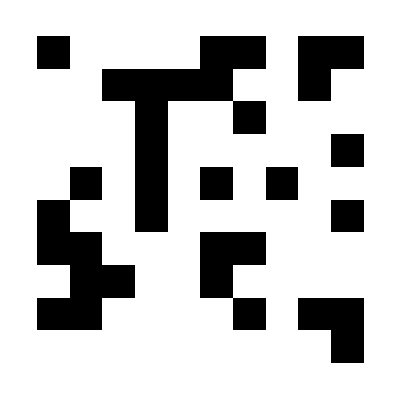

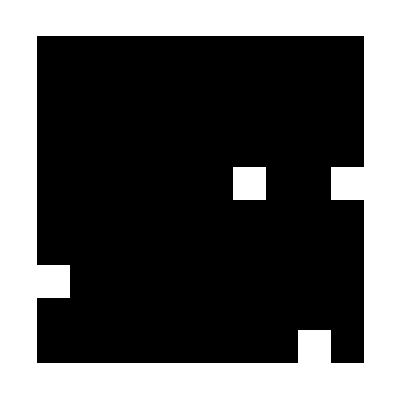

```mathematica
{primo,ultimo}= wolff2[1,0,10,1];
ArrayPlot[Partition[(primo+1)/2,10]]
ArrayPlot[Partition[(ultimo+1)/2,10]]
```